# Decaimiento del Higgs a dos fotones en VDDMM

```mathematica
$LoadPhi=True;
$LoadFeynArts=True;
Needs["HighEnergyPhysics`FeynCalc`"];
```

Loading FeynCalc from /home/felipe/.Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading PHI

WARNING! Your FeynArts installation is not complete or the version you have cannot be used with this version of FeynCalc.
FeynArts can be downloaded at www.feynarts.de

Loading FeynArts, see www.feynarts.de for documentation

FeynArts not found. Please install FeynArts, e.g., in
/home/felipe/.Mathematica
and reload FeynCalc
FeynArts can be downloaded from www.feynarts.de

## Definiciones

```mathematica
dm[mu_]:=DiracMatrix[mu]
dm[5]:=DiracMatrix[5]
ds[p_]:=DiracSlash[p]
mt[mu_,nu_]:=MetricTensor[mu,nu]
fv[p_,mu_]:=FourVector[p,mu]
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
sp[p_,q_]:=ScalarProduct[p,q]
li[mu_]:=LorentzIndex[mu]
prop[p_,m_]:=ds[p]+m
```

## Modelo Estandar

### Definiciones

```mathematica
q:=p-k1-k2
R:=p-k1
propW[p_,mu_,nu_]:=ⅈ*(-mt[mu,nu]+(fv[p,mu]*fv[p,nu])/MW^2)*FeynAmpDenominator[{p,MW}]
propf[p_,Mf_]:=ⅈ*prop[p,Mf]*FeynAmpDenominator[{p,Mf}]
HWW[mu_,nu_]:=ⅈ*g*MW*mt[mu,nu]
AAWW[mu_,nu_,rho_,sigma_]:=(-ⅈ*e^2)*(2*mt[mu,nu]*mt[rho,sigma]-mt[mu,rho]*mt[nu,sigma]-mt[mu,sigma]*mt[nu,rho])
AWW[p1_,p2_,p3_,mu_,nu_,rho_]:=(-ⅈ*e)*((fv[p3,mu]-fv[p2,mu])*mt[nu,rho]+(fv[p2,rho]-fv[p1,rho])*mt[mu,nu]+(fv[p1,nu]-fv[p3,nu])*mt[mu,rho])
Hff[Mf_]:=-ⅈ*(Mf*g)/(2*MW)
Att[mu_,Qf_]:=-ⅈ*e*Qf*dm[mu]
ϵA[p_,mu_]:=PolarizationVector[p,mu]
```

### Restricciones

```mathematica
onshell={sp[k1,k1]->0,sp[k2,k2]->0,sp[k1,k2]->MH^2/2};
```

## Interaccion triangulo con W

```mathematica
mHAA1a=Simplify[Contract[HWW[alpha,alpha].propW[p,alpha,beta].AWW[-k1,-R,p,mu,rho,beta].propW[R,rho,sig].AWW[-k2,-q,R,nu,gamma,sig].propW[q,gamma,alpha].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA1a=FullSimplify[mHAA1a/.onshell];
mHAA1b=Simplify[Contract[HWW[alpha,alpha].propW[p,alpha,beta].AWW[-k1,p+k1,-p,mu,rho,beta].propW[p+k1,rho,sig].AWW[-k2,p+k1+k2,-p-k1,nu,gamma,sig].propW[p+k1+k2,gamma,alpha].ϵA[k1,mu]*ϵA[k2,nu]]];
MHAA1b=FullSimplify[mHAA1b/.onshell];
```

## Interaccion de contacto con vertice AAWW

```mathematica
mHAA2=Simplify[Contract[HWW[alpha,alpha].propW[p,alpha,beta].AAWW[mu,nu,gamma,beta].propW[q,gamma,alpha].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA2=FullSimplify[mHAA2/.onshell];
```

## Interaccion triangulo con fermiones

```mathematica
Qt=2/3;
Qb=-1/3;
Qc=2/3;
Qtau=1;
```

#### Consideremos Mt, Mc, Mb, Mtau

```mathematica
mHAA3topa=Simplify[Contract[Nc*(-1)*Hff[Mt].Tr[Contract[propf[p,Mt].propf[q,Mt].Att[nu,Qt].propf[R,Mt].Att[mu,Qt]]].ϵA[k1,mu].ϵA[k2,nu]]];
mHAA3topb=Simplify[Contract[Nc*(-1)*Hff[Mt].Tr[Contract[propf[p,Mt].Att[mu,Qt].propf[p+k1,Mt].Att[nu,Qt].propf[p+k1+k2,Mt]]].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA3topa=FullSimplify[mHAA3topa/.onshell];
MHAA3topb=FullSimplify[mHAA3topb/.onshell];
```

```mathematica
mHAA3ba=Simplify[Contract[Nc*(-1)*Hff[Mb].Tr[Contract[propf[p,Mb].propf[q,Mb].Att[nu,Qb].propf[R,Mb].Att[mu,Qb]]].ϵA[k1,mu].ϵA[k2,nu]]];
mHAA3bb=Simplify[Contract[Nc*(-1)*Hff[Mb].Tr[Contract[propf[p,Mb].Att[mu,Qb].propf[p+k1,Mb].Att[nu,Qb].propf[p+k1+k2,Mb]]].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA3ba=FullSimplify[mHAA3ba/.onshell];
MHAA3bb=FullSimplify[mHAA3bb/.onshell];
```

```mathematica
mHAA3ca=Simplify[Contract[Nc*(-1)*Hff[Mc].Tr[Contract[propf[p,Mc].propf[q,Mc].Att[nu,Qc].propf[R,Mc].Att[mu,Qc]]].ϵA[k1,mu].ϵA[k2,nu]]];
mHAA3cb=Simplify[Contract[Nc*(-1)*Hff[Mc].Tr[Contract[propf[p,Mc].Att[mu,Qc].propf[p+k1,Mc].Att[nu,Qc].propf[p+k1+k2,Mc]]].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA3ca=FullSimplify[mHAA3ca/.onshell];
MHAA3cb=FullSimplify[mHAA3cb/.onshell];
```

```mathematica
mHAA3taua=Simplify[Contract[(-1)*Hff[Mtau].Tr[Contract[propf[p,Mtau].propf[q,Mtau].Att[nu,Qtau].propf[R,Mtau].Att[mu,Qtau]]].ϵA[k1,mu].ϵA[k2,nu]]];
mHAA3taub=Simplify[Contract[(-1)*Hff[Mtau].Tr[Contract[propf[p,Mtau].Att[mu,Qtau].propf[p+k1,Mtau].Att[nu,Qtau].propf[p+k1+k2,Mtau]]].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA3taua=FullSimplify[mHAA3taua/.onshell];
MHAA3taub=FullSimplify[mHAA3taub/.onshell];
```

## Integramos cada termino

```mathematica
IHAA1a=I*Simplify[PaVeReduce[OneLoop[p,MHAA1a]]]/.onshell;
IHAA1b=I*Simplify[PaVeReduce[OneLoop[p,MHAA1b]]]/.onshell;
```

```mathematica
IHAA2=I*Simplify[PaVeReduce[OneLoop[p,MHAA2]]]/.onshell;
```

```mathematica
IHAA3topa=I*Simplify[PaVeReduce[OneLoop[p,MHAA3topa]]]/.onshell;
IHAA3topb=I*Simplify[PaVeReduce[OneLoop[p,MHAA3topb]]]/.onshell;
IHAA3ba=I*Simplify[PaVeReduce[OneLoop[p,MHAA3ba]]]/.onshell;
IHAA3bb=I*Simplify[PaVeReduce[OneLoop[p,MHAA3bb]]]/.onshell;
IHAA3ca=I*Simplify[PaVeReduce[OneLoop[p,MHAA3ca]]]/.onshell;
IHAA3cb=I*Simplify[PaVeReduce[OneLoop[p,MHAA3cb]]]/.onshell;
IHAA3taua=I*Simplify[PaVeReduce[OneLoop[p,MHAA3taua]]]/.onshell;
IHAA3taub=I*Simplify[PaVeReduce[OneLoop[p,MHAA3taub]]]/.onshell;
```

```mathematica
IHAAWT=1/(64*π^4)*Simplify[IHAA1a+IHAA1b+IHAA2];
```

```mathematica
IHAAtopT=4/(64*π^4)*FullSimplify[IHAA3topa+IHAA3topb];
IHAAbT=4/(64*π^4)*FullSimplify[IHAA3ba+IHAA3bb];
IHAAcT=4/(64*π^4)*FullSimplify[IHAA3ca+IHAA3cb];
IHAAtauT=4/(64*π^4)*FullSimplify[IHAA3taua+IHAA3taub];
```

Test de Divergencias

```mathematica
div={A0[MW^2]->MW^2*Div,B0[0,MW^2,MW^2]->Div,B0[MH^2,MW^2,MW^2]->Div};
ansW1=FullSimplify[IHAA1a+IHAA1b]/.onshell;
ansW2=FullSimplify[IHAA2]/.onshell;
div1=Simplify[Coefficient[ansW1/.div,Div]]*Div;
div2=Simplify[Coefficient[ansW2/.div,Div]]*Div;
FullSimplify[div1+div2]
```

0

### Elimino las polarizaciones de los fotones

```mathematica
IHAAW=Coefficient[IHAAWT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
```

(e^2 g (6 MW^2 (MH^2-2 MW^2) C_0(0,0,MH^2,MW^2,MW^2,MW^2)-MH^2-6 MW^2) (MH^2 g^munu-2 k_2^mu k_1^nu))/(16 π^2 MH^2 MW)

```mathematica
IHAAtopT=Coefficient[IHAAtopT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
IHAAbT=Coefficient[IHAAbT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
IHAAcT=Coefficient[IHAAcT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
IHAAtauT=Coefficient[IHAAtauT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
```

-((e^2 g Mt^2 Nc Qt^2 ((MH^2-4 Mt^2) C_0(0,0,MH^2,Mt^2,Mt^2,Mt^2)-2) (MH^2 g^munu-2 k_2^mu k_1^nu))/(8 π^2 MH^2 MW))

(e^2 g Mb^2 Nc Qb^2 ((4 Mb^2-MH^2) C_0(0,0,MH^2,Mb^2,Mb^2,Mb^2)+2) (MH^2 g^munu-2 k_2^mu k_1^nu))/(8 π^2 MH^2 MW)

(e^2 g Mc^2 Nc Qc^2 ((4 Mc^2-MH^2) C_0(0,0,MH^2,Mc^2,Mc^2,Mc^2)+2) (MH^2 g^munu-2 k_2^mu k_1^nu))/(8 π^2 MH^2 MW)

-((e^2 g Mtau^2 Qtau^2 ((MH^2-4 Mtau^2) C_0(0,0,MH^2,Mtau^2,Mtau^2,Mtau^2)-2) (MH^2 g^munu-2 k_2^mu k_1^nu))/(8 π^2 MH^2 MW))

### Introduzco el cambio de variables βw->(4 MW^2)/MH^2 y βt->(4 Mt^2)/MH^2

```mathematica
var1:={C0[0,0,MH^2,MW^2,MW^2,MW^2]->-(2/MH^2)*(XW-2-3*βw)/(3*βw*(2-βw))}
var2:={C0[0,0,MH^2,Mt^2,Mt^2,Mt^2]->-(2/MH^2)*((XFt+2*βt)/(2*βt))*1/(βt-1)}
var3:={C0[0,0,MH^2,Mb^2,Mb^2,Mb^2]->-(2/MH^2)*((XFb+2*βb)/(2*βb))*1/(βb-1)}
var4:={C0[0,0,MH^2,Mc^2,Mc^2,Mc^2]->-(2/MH^2)*((XFc+2*βc)/(2*βc))*1/(βc-1)}
var5:={C0[0,0,MH^2,Mtau^2,Mtau^2,Mtau^2]->-(2/MH^2)*((XFtau+2*βtau)/(2*βtau))*1/(βtau-1)}
var6:={MH->√((4 MW^2)/βw)}
var7:={MH->√((4 Mt^2)/βt)}
var8:={MH->√((4 Mb^2)/βb)}
var9:={MH->√((4 Mc^2)/βc)}
var10:={MH->√((4 Mtau^2)/βtau)}
```

### Simplificamos la expresion

```mathematica
IHAAWf=FullSimplify[IHAAW/.var1/.var6/.{βw->4*MW^2/MH^2}]
```

-(e^2 g XW (MH^2 g^munu-2 k_2^mu k_1^nu))/(32 π^2 MW)

```mathematica
IHAATtop=FullSimplify[IHAAtopT/.var2/.var7/.{βt->4*Mt^2/MH^2}]
IHAATb=FullSimplify[IHAAbT/.var3/.var8/.{βb->4*Mb^2/MH^2}]
IHAATc=FullSimplify[IHAAcT/.var4/.var9/.{βc->4*Mc^2/MH^2}]
IHAATtau=FullSimplify[IHAAtauT/.var5/.var10/.{βtau->4*Mtau^2/MH^2}]
```

-(e^2 g Nc Qt^2 XFt (MH^2 g^munu-2 k_2^mu k_1^nu))/(32 π^2 MW)

-(e^2 g Nc Qb^2 XFb (MH^2 g^munu-2 k_2^mu k_1^nu))/(32 π^2 MW)

-(e^2 g Nc Qc^2 XFc (MH^2 g^munu-2 k_2^mu k_1^nu))/(32 π^2 MW)

-(e^2 g Qtau^2 XFtau (MH^2 g^munu-2 k_2^mu k_1^nu))/(32 π^2 MW)

### Matriz M

```mathematica
MAT=Simplify[IHAAWf+IHAATtop+IHAATb+IHAATc+IHAATtau]
```

-1/(32 π^2 MW)e^2 g (MH^2 g^munu-2 k_2^mu k_1^nu) (Nc (Qb^2 XFb+Qc^2 XFc+Qt^2 XFt)+Qtau^2 XFtau+XW)

### Matriz M^2

```mathematica
MMT=Simplify[Contract[MAT.MAT]];
MMSM=FullSimplify[MMT/.onshell/.{e->√(4*π*α)}/.{g->√((8*GF*MW^2)/(√2))}]
```

1/(4 √2 π^2)α^2 GF MH^4 (Nc (Qb^2 XFb+Qc^2 XFc+Qt^2 XFt)+Qtau^2 XFtau+XW)^2

### Ancho de decaimiento

```mathematica
AnchoHAA[XFt_,XFb_,XFc_,XFtau_,XW_]=(4π)/(64*π^2 MH)MMSM*(1/2)
```

1/(128 √2 π^3)α^2 GF MH^3 (Nc (Qb^2 XFb+Qc^2 XFc+Qt^2 XFt)+Qtau^2 XFtau+XW)^2

```mathematica
f[x_]:=Piecewise[{{(ArcSin[√(1/x)])^2,x≥1},{-1/4*(Log[(1+√(1-x))/(1-√(1-x))-ⅈ*π])^2,x<1}}]
XW[β_]:=2+3*β+3*β*(2-β)*f[β]
XF[β_]:=-2*β*(1+(1-β)*f[β])
XFt[a_]:=XF[a]
XFb[a_]:=XF[a]
XFc[a_]:=XF[a]
XFtau[a_]:=XF[a]
```

```mathematica
Re[Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mtau=1.777,MW=80.385,GF=1.2057*10^-5,Nc=3,α=1/137},AnchoHAA[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2]]]]
```

9.64683×10^-6

```mathematica
HAAcalc=9.708*10^-6;
```

```mathematica
error=Abs[Re[Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mtau=1.777,MW=80.385,GF=1.2057*10^-5,Nc=3,α=1/137},AnchoHAA[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2]]]]-HAAcalc]/HAAcalc*100
```

0.630059

## Modelo VHDM

### Definiciones

```mathematica
propV[p_,mu_,nu_]:=ⅈ*(-mt[mu,nu]+(fv[p,mu]*fv[p,nu])/MVP^2)*FeynAmpDenominator[{p,MVP}]
HVV[mu_,nu_]:=(ⅈ*2*MW)/g*λ2*mt[mu,nu]
AVV[p1_,p2_,p3_,mu_,nu_,rho_]:=AWW[p1,p2,p3,mu,nu,rho]
AAVV[mu_,nu_,rho_,sigma_]:=AAWW[mu,nu,rho,sigma]
```

## Interaccion triangulo con V

```mathematica
mHAA4a=Simplify[Contract[HVV[alpha,alpha].propV[q,gamma,alpha].AVV[-k2,-q,R,nu,gamma,sig].propV[R,rho,sig].AVV[-k1,-R,p,mu,rho,beta].propV[p,alpha,beta].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA4a=Simplify[mHAA4a/.onshell];
mHAA4b=Simplify[Contract[HVV[alpha,alpha].propV[p,alpha,beta].AVV[-k1,p+k1,-p,mu,rho,beta].propV[p+k1,rho,sig].AVV[-k2,p+k1+k2,-p-k1,nu,gamma,sig].propV[p+k1+k2,gamma,alpha].ϵA[k1,mu]*ϵA[k2,nu]]];
MHAA4b=FullSimplify[mHAA4b/.onshell];
```

## Interaccion de contacto vertice AAVV

```mathematica
mHAA5=Simplify[Contract[HVV[alpha,alpha].propV[p,alpha,beta].AAVV[mu,nu,gamma,beta].propV[q,gamma,alpha].ϵA[k1,mu].ϵA[k2,nu]]];
MHAA5=FullSimplify[mHAA5/.onshell];
```

## Integramos cada termino

```mathematica
IHAA4a=I*Simplify[PaVeReduce[OneLoop[p,MHAA4a]]]/.onshell;
IHAA4b=I*Simplify[PaVeReduce[OneLoop[p,MHAA4b]]]/.onshell;
```

```mathematica
IHAA5=I*Simplify[PaVeReduce[OneLoop[p,MHAA5]]]/.onshell;
```

```mathematica
IHAAVT=1/(64*π^4)*FullSimplify[(IHAA4a+IHAA4b+IHAA5)]
```

(e^2 λ2 MW (6 MVP^2 (MH^2-2 MVP^2) C_0(0,0,MH^2,MVP^2,MVP^2,MVP^2)-MH^2-6 MVP^2) (MH^2 ε(k_1)·ε(k_2)-2 k_1·ε(k_2) k_2·ε(k_1)))/(8 π^2 g MH^2 MVP^2)

Test de Divergencia

```mathematica
divV={A0[MVP^2]->MVP^2*Div,B0[0,MVP^2,MVP^2]->Div,B0[MH^2,MVP^2,MVP^2]->Div};
ansV1=FullSimplify[IHAA4a+IHAA4b]/.onshell;
ansV2=FullSimplify[IHAA5]/.onshell;
div3=Simplify[Coefficient[ansV1/.divV,Div]]*Div;
div4=Simplify[Coefficient[ansV2/.divV,Div]]*Div;
FullSimplify[div3+div4]
```

0

### Elimino las polarizaciones de los fotones

```mathematica
IHAAV=Coefficient[IHAAVT,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])
```

1/(8 π^2 g MH^2 MVP^2)e^2 λ2 MW (6 MVP^2 (MH^2-2 MVP^2) C_0(0,0,MH^2,MVP^2,MVP^2,MVP^2)-MH^2-6 MVP^2) (MH^2 g^munu-2 k_2^mu k_1^nu)

### Introduzco el cambio de variables βV->(4 MV^2)/MH^2

```mathematica
var11:={C0[0,0,MH^2,MVP^2,MVP^2,MVP^2]->-(2/MH^2)*(XV-2-3*βV)/(3*βV*(2-βV))}
var12:={MH->√((4 MVP^2)/βV)}
```

```mathematica
IHAAVf=FullSimplify[IHAAV/.var11/.var12/.{βV->4*MVP^2/MH^2}]
```

-(e^2 λ2 MW XV (MH^2 g^munu-2 k_2^mu k_1^nu))/(16 π^2 g MVP^2)

### Sumamos las amplitudes del SM y VHDMM

```mathematica
IHAATOT=FullSimplify[IHAAVf+MAT];
```

```mathematica
MMTT=FullSimplify[Contract[IHAATOT.IHAATOT]]/.onshell;
MMBSM=FullSimplify[MMTT/.onshell/.{e->√(4*π*α)}/.{g->√((8*GF*MW^2)/(√2))}](*/.{λ2->λL+2*((MV1^2-MVP^2)/vv^2)}*)
```

1/(32 √2 π^2 GF MVP^4)α^2 MH^4 (2 √2 GF MVP^2 (Nc (Qb^2 XFb+Qc^2 XFc+Qt^2 XFt)+Qtau^2 XFtau+XW)+λ2 XV)^2

### Ancho total

```mathematica
AnchoHAAV[XFt_,XFb_,XFc_,XFtau_,XW_,XV_]=(4π)/(64*π^2 MH)MMBSM*(1/2)/.{GF->1/(√2*v^2)}
```

(α^2 MH^3 v^2 ((2 MVP^2 (Nc (Qb^2 XFb+Qc^2 XFc+Qt^2 XFt)+Qtau^2 XFtau+XW))/v^2+λ2 XV)^2)/(1024 π^3 MVP^4)

```mathematica
XV[β_]:=XW[β]
```

```mathematica
Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mtau=1.777,MW=80.385,,MVP=600,MV1=600,GF=1.2057*10^-5,Nc=3,α=1/137,λL=0,vv=242.17},Re[AnchoHAAV[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2],XV[4*MVP^2/MH^2]]]]
```

9.64683×10^-6

```mathematica
Re[Block[{vv=242.17,MH=125,Mt=172.5,MW=80.385,Mb=4.25,Mc=1.23,Mtau=1.777,MV1=100,MVP=1000,GF=1.2057*10^-5,Nc=3,α=1/137,λL=0},AnchoHAAV[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2],XV[4*MVP^2/MH^2]]]]
```

3.0029×10^-8

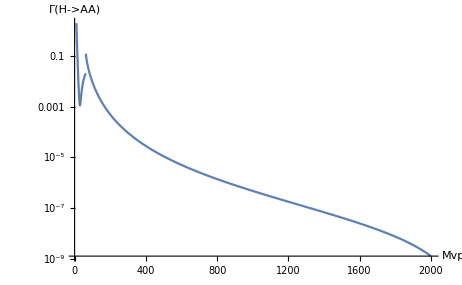

```mathematica
Block[{vv=243,MH=125,Mt=172.5,MW=80.385,Mb=4.25,Mc=1.23,Mtau=1.777,MV1=500,MVP=200,GF=1.2057*10^-5,Nc=3,α=1/137,λL=0.5},LogPlot[Re[AnchoHAAV[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFtau[4*Mtau^2/MH^2],XW[4*MW^2/MH^2],XV[4*MVP^2/MH^2]]],{MVP,10,2000},AxesLabel->{"Mvp","Γ(H->AA)"}]]
```